# Hyperspherical Pseudorandom Vectors

Technical Report, GSI Technology

Brian Beckman

Technology Fellow
October, 2023
(Adapted from my work previously done at Amazon Robotics)

Abstract

We need uniformly distributed pseudorandom vectors in d≥2 dimensions for simulation, estimation, control, machine learning, optimization, search, test generation, and more. With vectors rooted at the origin, uniformly distributed means with a constant likelihood of generating a vector endpoint anywhere inside a d-ball. The number of dimensions needed can be very large, corresponding to the number of degrees of freedom in a physical system or the number of weights in a neural network. Rejection sampling in the d-cube is not feasible for even moderate numbers of dimensions because almost all vector endpoints are in the corners. For example, in twenty-seven dimensions, only one in a trillion vector endpoints in the d-cube is in the d-ball.

We demonstrate two computational methods that scale efficiently to high dimensionality for generating pseudorandom vectors uniformly distributed on the unit d-sphere (surface of the unit hypersphere) and in the unit d-ball (interior of the unit hypersphere). Though neither method is novel, descriptions available to me are unsatisfactory. The contributions of this note are proofs, executable specifications of algorithms, and numerical demonstrations.

## DEFINITIONS

The unit d-ball is the interior of a hypersphere: the set of all real d-vectors rooted at the origin, (x_1,x_2,…,x_d)∈ℝ^d, such that x_1^2+x_2^2+⋯+x_d^2<1. The unit d-sphere is the boundary of the d-ball, that is, the set of all real d-vectors such that x_1^2+x_2^2+⋯+x_d^2=1.

The unit d-cube is the set of all real d-vectors such that each coordinate is absolutely bounded by unity, inclusively, that is, where -1≤x_(i∈[1..d])≤1. The unit d-ball, d-sphere, and d-cube are also said to have radius 1, diameter 2.

We do not distinguish between the mathematical procedure of sampling a distribution and the computational procedure of generating pseudorandoms according to a distribution. Likewise, we do not distinguish between mathematical true randoms and computational pseudorandoms.

Generating randoms uniformly means the same as generating uniform randoms. Generating randoms symmetrically means the same as generating symmetric randoms.

## UNIFORM RANDOMS IN THE D-CUBE

Given an efficient method for generating uniform random scalars in the real interval [-1..1] — in the 1-cube — it is easy and efficient to generate rectangularly symmetric, uniform randoms in the d-cube: generate randoms for each of the d coordinates independently.

Can we generate spherically symmetric uniform randoms starting with rectangularly symmetric, uniform randoms? Yes, but it takes some care to do it efficiently. Rejection methods (generating rectangularly symmetric, uniform randoms and then throwing out those that are not in the d-ball) are crippled: only one in a trillion endpoints in the 27-cube is also in the 27-ball; the ratio gets worse exponentially as d increases.

Consider points (vector endpoints) uniformly distributed in the unit 2-cube, i.e., the unit square. The resulting (x,y) pairs are not uniform with angle, therefore not spherically symmetric. The following diagrams illustrate: here are points uniformly distributed in the 2-ball:

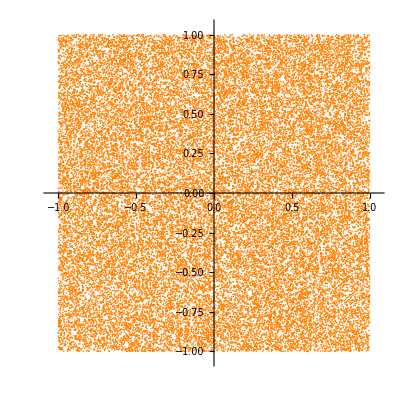

```mathematica
show2D$[points_,γ_:1.05]:=
ListPlot[Style[points,Orange],
PlotRange->{{-γ,γ},{-γ,γ}},
AspectRatio->1];
show3D$[points_,γ_:1.05]:=
ListPointPlot3D[Style[points,Orange],
PlotRange->{{-γ,γ},{-γ,γ},{-γ,γ}},
BoxRatios->{1,1,1}];
twoCubeRandoms$=
RandomVariate[
UniformDistribution[{{-1,1},{-1,1}}],
40000];
show2D$[twoCubeRandoms$]
```

There are too many points in the corners, at ArcTan[1,1]=0.7854, ArcTan[-1,1]=2.3562 and their negatives:

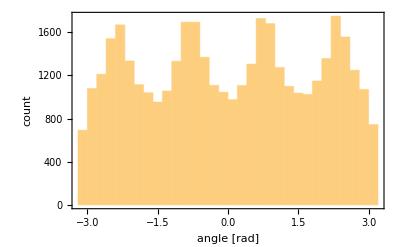

```mathematica
Histogram[MapThread[ArcTan,
{First/@twoCubeRandoms$,
First/@Rest/@twoCubeRandoms$}],
Frame->True,FrameLabel->{{"count",""},{"angle [rad]","Angle Distribution of \n40,000 Uniformly Random 2-Vectors"}}]
```

### REJECTION METHOD: IMPRACTICAL

We could reject, i.e., remove points in the unit d-cube that are not in the unit d-ball. Those would be points with radial component — Euclidean norm — greater than 1. However, rejection does not scale. As d grows, the number of corners goes up as 2^d and almost all points are outside the unit d-ball, i.e., in the corners. To show this, compute the ratio of the volume of a unit d-ball to the volume of a unit d-cube.

What is the volume of a unit d-cube? Answer: 2^d. What is the volume of a unit d-ball? (see https://en.wikipedia.org/wiki/Volume_of_an_n-ball)

Answer: integer d:

```mathematica
ClearAll[vBall];
vBall[d_,r_:1]:=Piecewise[{{With[{k=d/2},π^k/(k!)r^d], Mod[d,2]===0}, {With[{k=(d-1)/2},(2k!(4π)^k)/(d!)r^d], Mod[d,2]===1}}];
Table[<|"dimension"->d,"ball volume"->vBall[d], "cube volume"->2^d,"cube/ball ratio"->N[2^d/vBall[d]]|>,{d,1,10}]//MatrixForm
```

(<|dimension→1,ball volume→2,cube volume→2,cube/ball ratio→1.|>
<|dimension→2,ball volume→π,cube volume→4,cube/ball ratio→1.27324|>
<|dimension→3,ball volume→(4 π)/3,cube volume→8,cube/ball ratio→1.90986|>
<|dimension→4,ball volume→π^2/2,cube volume→16,cube/ball ratio→3.24228|>
<|dimension→5,ball volume→(8 π^2)/15,cube volume→32,cube/ball ratio→6.07927|>
<|dimension→6,ball volume→π^3/6,cube volume→64,cube/ball ratio→12.3846|>
<|dimension→7,ball volume→(16 π^3)/105,cube volume→128,cube/ball ratio→27.0913|>
<|dimension→8,ball volume→π^4/24,cube volume→256,cube/ball ratio→63.0742|>
<|dimension→9,ball volume→(32 π^4)/945,cube volume→512,cube/ball ratio→155.222|>
<|dimension→10,ball volume→π^5/120,cube volume→1024,cube/ball ratio→401.543|>)

With gamma, arbitrary real dimensions:

```mathematica
ClearAll[vBall];
vBall[d_,r_:1]:=(π^(d/2)r^d)/Gamma[1+d/2];
```

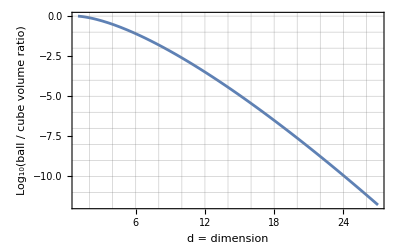

```mathematica
Plot[Log10[vBall[d]/2^d],{d,1,27},
Frame->True,GridLines->All, FrameLabel->{{"Log_10(ball / cube volume ratio)",""},{"d = dimension","Volume Ratio of Unit d-ball to Unit d-cube"}}]
```

The ratio of ball-to-cube volume in 27 dimensions is one trillionth, so the rejection method generates a trillion times more points than it keeps. Rejection is impractical for even moderately large d.

## RADIAL SYMMETRY

Observe that a multivariate Gaussian or multinormal distribution is radially symmetric. Sampling x from (ⅇ^(-x^2/2))/(√(2 π)), and y similarly, then noticing that x and y are independent (the probability of their occurring simultaneously is the product of their individual probabilities), we get (ⅇ^(-x^2/2))/(√(2 π))×(ⅇ^(-y^2/2))/(√(2 π))=(ⅇ^(-1/2 (x^2+y^2)))/(2 π). A similar construction extends to any number of dimensions.

The multinormal distribution is radially symmetric because it depends only on the radius squared, x^2+y^2, not on the azimuth angle. But it is not radially uniform, as the following figure demonstrates:

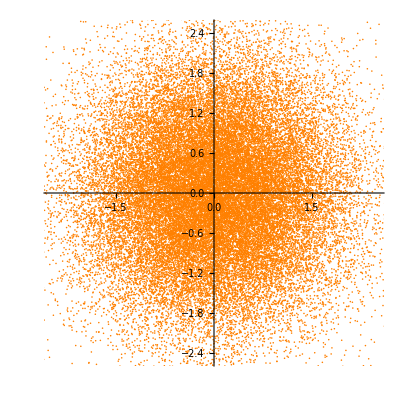

```mathematica
show2D$[RandomVariate[
MultinormalDistribution[IdentityMatrix[2]],40000],2.5]
```

## RADIAL UNIFORMITY

Due to radial symmetry, normalizing d-vectors from the d-ball produces d-vectors uniform on the d-sphere (surface), not in the d-ball (interior). For example, the following points are uniformly distributed on the 2-sphere:

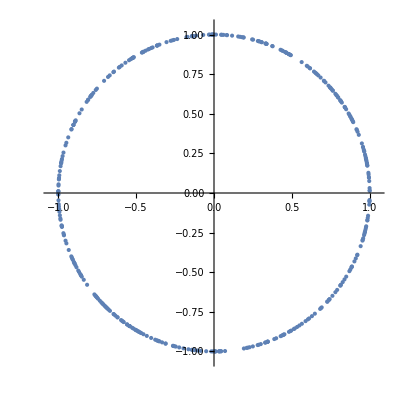

```mathematica
With[{γ=1.05},
ListPlot[Normalize/@
RandomVariate[
MultinormalDistribution[IdentityMatrix[2]],400],
PlotRange->{{-γ,γ},{-γ,γ}},AspectRatio->1]]
```

## FROM SYMMETRY TO UNIFORMITY

Now that we can generate uniform randoms on the d-sphere, the boundary of the d-ball, can we fill the interior uniformly? We show below two ways: a geometrical construction and a statistical construction.

## GEOMETRICAL CONSTRUCTION

Reduce the lengths of vectors radially, pulling their end-points toward the center, preserving radial symmetry. But how to achieve spherical uniformity? Shrinking vectors by a uniform random factor in [0,1] will not work. The results will be too sparse in outer zones and too dense in inner zones:

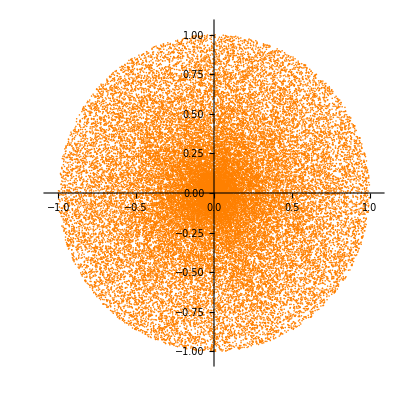

```mathematica
show2D$@With[{count=40000},With[{pointsOnSphere=
Normalize/@
RandomVariate[
MultinormalDistribution[IdentityMatrix[2]],count],
scalar=
RandomVariate[UniformDistribution[{0,1}],count]},
MapThread[Times,{pointsOnSphere,scalar}]]]
```

If points were uniformly distributed with radius r, the volume density would be proportional to r^-d=1/r^d, approaching infinity as r→0. If points were uniformly distributed in r^(1/d), then the volume density would be constant: that is what we want.

### sampleDBall

```mathematica
ClearAll[sampleDBall];
sampleDBall[d_,n_]:=
With[{
pointsOnSphere=
Normalize/@
RandomVariate[
MultinormalDistribution[IdentityMatrix[d]],n],
scalar=
Power[
RandomVariate[UniformDistribution[],n],
1/d]},
MapThread[Times,{pointsOnSphere,scalar}]];
```

The following plots illustrate points uniformly distributed in radius in two and three dimensions, and thus uniformly distributed in the 2-ball and in the 3-ball, respectively:

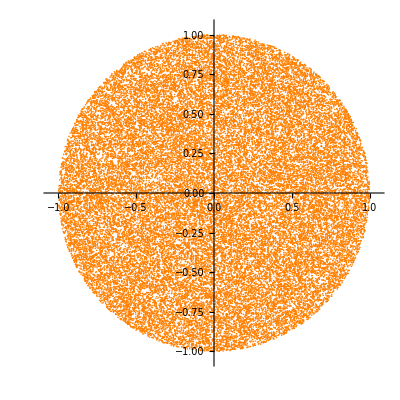

```mathematica
show2D$[sampleDBall[2,40000]]
```

```mathematica
show3D$[sampleDBall[3,40000]]
```

-Graphics3D-

## UNIFORMITY STATISTICS

We exhibit two ways to collect statistics on a sample: by shell and by cubie. From the statistics, we can calculate average point density (per unit d-volume) and check that it is uniform. The shell method counts points that lie within d-shells of constant volume. The cubie method counts points in elementary (small) d-cubes of constant volume. The shell method is robust and practical. The cubie method is obvious but naive, inaccurate, and impractical for dimensions more than three. The rest of this section demonstrates.

### BY SHELL

The volume of a d-ball of radius ρ is proportional to ρ^d. Incrementing ρ^d by a constant Δv produces a sequence of shells of equal volumes (constant Δv is proportional to constant Δ-volume). Thus, we may index shells by integer multiples of Δv: shell number Ceiling[ρ^d,Δv] contains the point p with Euclidean norm ρ.

In a large sample, we expect the mean number of vectors with endpoints in each shell to be drawn from the same, uniform distribution. The Chi-squared test for a uniform distribution demands that the standard deviation of endpoint counts in each shell be approximately equal to the square root of the mean of the endpoint counts in each shell. That observation gives us a pragmatic, “eyeball” test for uniformity. If the standard deviation is unreasonably far from the square root of the mean, we likely have a non-uniform source distribution.

The following are numerical statistics across 100 shells of equal volume for one million spherically uniform randoms in each of two, three, six, sixteen, and 276 dimensions. The expected mean number of points in each shell is 10000=1000000/100, and the expected standard deviations of the counts is √10000=100. The empirical standard deviations agree reasonably well with the expected.

A rigorous Chi-squared test would give the probability that each shell is not drawn from the same uniform distribution, but the agreement between empirical and expected standard deviations is good enough that a rigorous Chi-squared test does not seem necessary.

### SAMPLED SHELL COUNTS

```mathematica
ClearAll[pairwise];
pairwise[fn_,list_List]:=
MapThread[fn,{Drop[list,-1],Rest[list]}];

ClearAll[pointsInShell2];
pointsInShell2[points_,d_,dr_]:=
GroupBy[points,p↦Ceiling[Norm[p]^d,dr]];

ClearAll[sampledShellCounts2];
sampledShellCounts2[deltaR_:0.01,d_:2,n_:4000,sampler_:sampleDBall]:=
With[{points=sampler[d,n]},
With[{countsAssoc=Length/@pointsInShell2[points,d,deltaR]},
Values[countsAssoc]]];

ClearAll[countsStats];
countsStats[counts_]:=
With[{𝒟=counts},
With[{
tot=Plus@@𝒟,
μ=Mean@𝒟,
σ=N@StandardDeviation@𝒟,
min=Min[𝒟],
max=Max[𝒟],
P=Quiet@FindDistribution[𝒟]},
Column@{ListLinePlot[𝒟,PlotRange->Full,ImageSize->Medium,AxesLabel->{"Sample Id","Sampled Number of Counts"}],
Show[
Histogram[𝒟,Automatic,"PDF",PlotRange->Full,AxesLabel->"Distribution of Sampled Number of Counts"],
Plot[PDF[P,c],{c,min,max}],ImageSize->Medium],
<|"μ"->N@μ,"expected stddev"->N@Sqrt[μ],"n samples"->Length[counts],"actual stddev"->σ,"total"->tot,"min"->min,"max"->max|>}]];
```

#### TWO DIMENSIONS

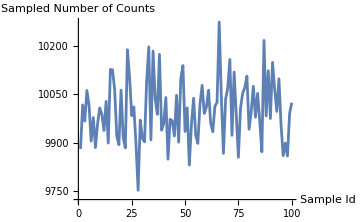
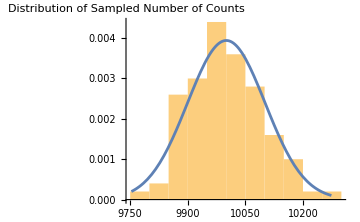
-Graphics-
-Graphics-
<|μ→10000.,expected stddev→100.,n samples→100,actual stddev→95.8446,total→1000000,min→9753,max→10274|>

```mathematica
countsStats[sampledShellCounts2[0.01,2,1000000]]
```

#### THREE DIMENSIONS

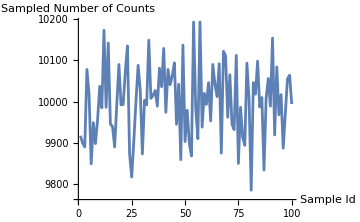
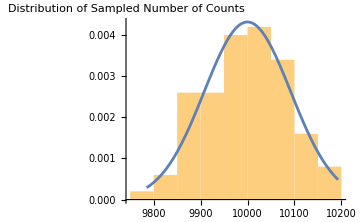
-Graphics-
-Graphics-
<|μ→10000.,expected stddev→100.,n samples→100,actual stddev→89.132,total→1000000,min→9785,max→10193|>

```mathematica
countsStats[sampledShellCounts2[0.01,3,1000000]]
```

#### SIX DIMENSIONS

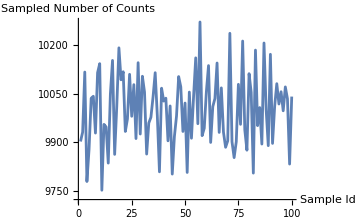
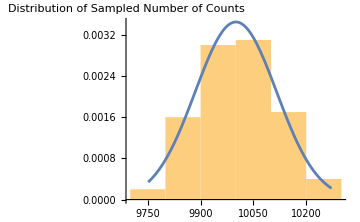
-Graphics-
-Graphics-
<|μ→10000.,expected stddev→100.,n samples→100,actual stddev→111.42,total→1000000,min→9751,max→10272|>

```mathematica
countsStats[sampledShellCounts2[0.01,6,1000000]]
```

#### SIXTEEN DIMENSIONS

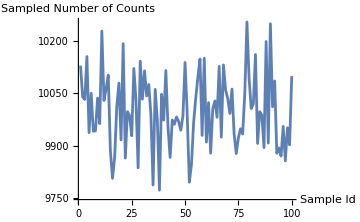
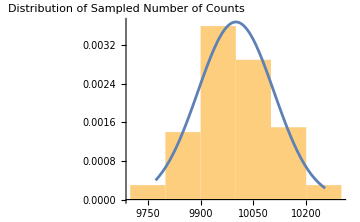
-Graphics-
-Graphics-
<|μ→10000.,expected stddev→100.,n samples→100,actual stddev→104.319,total→1000000,min→9772,max→10254|>

```mathematica
countsStats[sampledShellCounts2[0.01,16,1000000]]
```

#### 276 DIMENSIONS

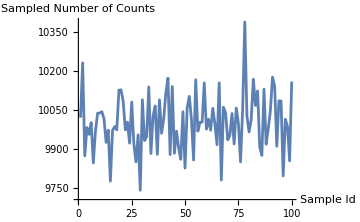
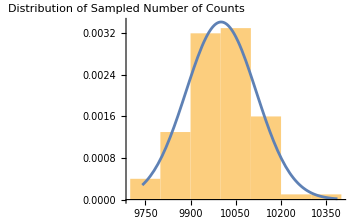
-Graphics-
-Graphics-
<|μ→10000.,expected stddev→100.,n samples→100,actual stddev→108.845,total→1000000,min→9740,max→10387|>

```mathematica
countsStats[sampledShellCounts2[0.01,276,1000000]]
```

### BY CUBIE

Statistics by cubie ignore geometry and count points in an evenly-spaced Cartesian grid of cubies. Statistics by shell are much faster and more informative because they honor geometry. Statistics by cubie do not scale to large d, where almost all the volume contains empty cubies. However, statistics by cubie are interesting for small d. The code is instructive, illustrating indexing by hashing cubie coordinates in a Mathematica Association, similar to a Python dictionary or to a Clojure hashmap.

Find the cubie boundaries near a point x. Boundary tuples are the keys of the hash table. Every point within a certain cubie will hash to the same key.

```mathematica
ClearAll[cellBoundaryTuple];
cellBoundaryTuple[x_,δ_]:=
With[{f=Floor[x,δ],c=Ceiling[x,δ]},
{f,c}];
```

Make a function of an existing hash table and a point, closed over a given cubie size δ. Locate the cubie of the point in the hash table and increment the cubie’s counts.

```mathematica
ClearAll[makeCubifer];
makeCubifer[δ_]:=
Function[{dict,point},
Module[{temp=dict},
With[{key=cellBoundaryTuple[point,δ]},
With[{val=temp[key]},
With[{test=Head[val]},
If[Missing===test,
AssociateTo[temp,key->1],
temp[key]++]]]];
temp]];
```

Visualize cubies — red for small counts, indigo for large counts.

```mathematica
ClearAll[cubiePolygon];
Module[{},
cubiePolygon[{xyLeft_,xyRight_},value_,maxVal_,minVal_]:=
With[{xLeft=xyLeft[[1]],xRight=xyRight[[1]],
yBottom=xyLeft[[2]],yTop=xyRight[[2]]},
{Hue[(value-minVal)/(maxVal-minVal)],Polygon[{{xLeft,yBottom},{xRight,yBottom},
{xRight,yTop},{xLeft,yTop}}]}]];
ClearAll[illustrateCubifers];
illustrateCubifers[δR_:0.1,d_:2,n_:4000]:=
With[{sample=sampleDBall[d,n]},
With[{kvs=Fold[makeCubifer[δR],<||>,sample]},
With[{keys=Keys[kvs],values=Values[kvs]},
With[{cubieArea=Times@@(keys[[1,2]]-keys[[1,1]])},
Print[<|"values"->Short[values],"sum"->Plus@@values, 
"number of cubies"->Length[keys],"cubie area"->cubieArea,
"point densities"->Short[values/cubieArea],
"avg point density"->Mean[values/cubieArea],
"stddev point density"->StandardDeviation[values/cubieArea]|>];
With[{vx=Max[values],vn=Min[values],len=Length[values]},
MapThread[cubiePolygon,{keys,values,
ConstantArray[vx,len],
ConstantArray[vn,len]}]]]]]]
```

<|values→{35,36,38,33,30,45,38,28,34,27,45,31,33,31,35,38,25,«3213»,11,2,4,4,6,5,2,2,4,3,1,2,3,4,1,1,1},sum→100000,number of cubies→3247,cubie area→0.001,point densities→{35000.,36000.,«3243»,1000.,1000.},avg point density→30797.7,stddev point density→7114.07|>

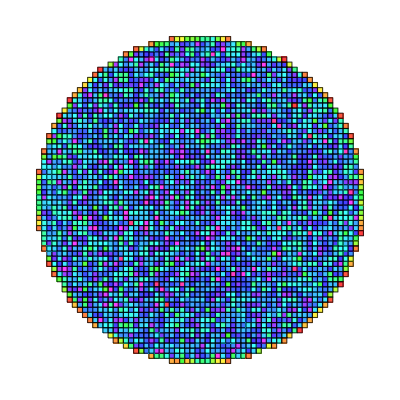

```mathematica
Graphics[{Opacity[0.75],EdgeForm[Black],illustrateCubifers[0.001^(1/2),2,100000]}]
```

```mathematica
ClearAll[sampledCubieCounts];
sampledCubieCounts[δR_:0.1,d_:2,n_:4000]:=
Module[{volumeRatio=N[vBall[d]/2^d]},
Module[{pctCubiesInTheBall=100volumeRatio,
numCubiesInTheBall=δR^-d volumeRatio},
Print[<|"Number of Cubies"->δR^-d,"Pct cubies in the d-ball"->pctCubiesInTheBall,"mean # points per cubie in the ball"->n/numCubiesInTheBall|>];
Module[{cubieHash=Fold[makeCubifer[δR],<||>,sampleDBall[d,n]]},
Print[Length@Keys[cubieHash]];
Values[cubieHash]]]];
```

In the following demonstrations, we consider n=100000 vector endpoints, restricting the sizes of cubies to the d-th root of 0.001 so that the total number of cubies is 1000; any more and the simulations are uncomfortably slow.

What is the expected mean number of points per cubie inside the ball? Note that approximately 1000(vBall(d))/2^d cubies are inside the ball and hold all 100000 points.

The number of cubies inside the d-ball is approximately 1000(vBall(d))/2^d and the number outside is about 1000(2^d-vBall(d))/2^d With more than 1000 cubies, the computations are too slow. We show results for two, three, six, and twenty-seven dimensions:

#### TWO DIMENSIONS

<|Number of Cubies→1000.,Pct cubies in the d-ball→78.5398,mean # points per cubie in the ball→127.324|>

3248

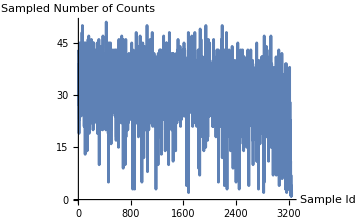
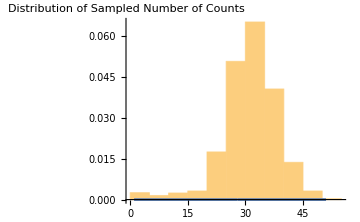
-Graphics-
-Graphics-
<|μ→30.7882,expected stddev→5.54871,n samples→3248,actual stddev→7.20106,total→100000,min→1,max→51|>

```mathematica
countsStats[sampledCubieCounts[0.001^(1/2),2,100000]]
```

There are already, even in two dimensions, a noticeable number of deficiently populated cubies (the tail to the left of the peak above). These are the cubies crossing the circle and in the corners outside the circle.

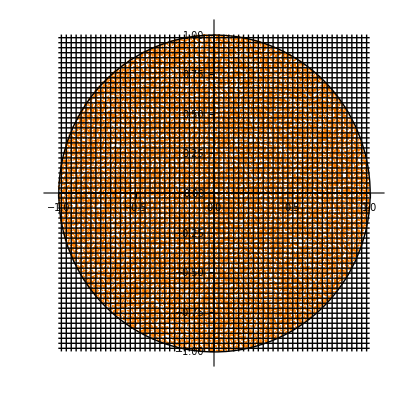

```mathematica
Show[show2D$[sampleDBall[2,40000]],Graphics[Circle[]],
Graphics@Line[{{#,-1},{#,1}}]&/@Range[0,1,0.001^(1/2)],
Graphics@Line[{{-1,#},{1,#}}]&/@Range[0,1,0.001^(1/2)],
Graphics@Line[{{#,-1},{#,1}}]&/@Range[0,-1,-0.001^(1/2)],
Graphics@Line[{{-1,#},{1,#}}]&/@Range[0,-1,-0.001^(1/2)]]
```

#### THREE DIMENSIONS

<|Number of Cubies→1000.,Pct cubies in the d-ball→52.3599,mean # points per cubie in the ball→190.986|>

{23,30,22,32,25,25,25,25,26,21,23,22,32,23,25,30,21,26,21,27,25,23,23,27,28,20,21,23,30,26,27,26,17,28,22,25,27,20,17,14,26,25,24,28,30,21,18,29,7,33,27,22,33,32,22,16,20,30,26,27,23,24,33,21,17,36,24,19,27,27,19,22,25,22,33,23,26,10,22,33,24,26,21,30,22,18,25,23,20,18,16,8,28,28,25,27,20,19,8,27,23,16,29,24,10,20,22,21,32,11,20,26,39,14,26,22,27,17,24,16,31,17,14,28,26,16,23,26,27,16,28,26,18,18,24,25,24,24,18,34,21,30,30,27,26,26,32,23,19,30,24,21,33,18,19,25,27,23,24,22,21,25,23,20,32,23,28,25,33,28,24,27,26,20,23,14,23,27,22,23,18,26,17,6,25,24,30,20,30,22,17,27,25,26,30,22,28,13,22,18,25,22,18,25,22,29,26,23,23,27,12,31,18,26,21,20,18,12,12,27,22,32,31,23,23,24,30,26,19,25,3,23,34,28,31,34,39,33,25,23,18,23,19,23,20,27,31,29,24,20,23,24,14,34,5,17,26,25,31,20,19,33,21,30,40,22,29,29,24,27,12,22,24,23,20,21,23,21,23,30,28,27,25,22,35,28,28,26,25,25,25,23,16,26,25,33,15,30,21,27,24,14,23,21,16,23,15,28,32,19,17,28,31,21,24,27,21,21,18,25,31,31,31,19,23,26,24,25,26,24,24,24,22,21,30,19,18,19,23,23,14,22,29,28,29,28,22,26,20,11,20,23,13,19,35,19,11,22,21,32,26,19,33,30,36,25,28,23,31,18,26,32,25,18,28,4,30,25,32,26,19,26,7,26,29,33,25,17,25,40,19,20,11,15,19,23,29,29,23,31,27,18,17,24,29,29,19,33,29,26,20,30,20,23,33,18,31,36,21,30,24,24,22,21,12,25,30,23,19,25,11,15,23,21,28,16,25,18,21,16,28,23,22,27,24,19,23,34,30,26,25,21,13,27,30,20,25,27,21,22,29,28,15,32,28,18,26,26,35,18,18,26,26,13,17,29,25,21,24,31,24,27,16,27,28,34,19,30,28,25,19,29,26,32,20,20,35,26,20,27,21,33,32,28,21,27,22,32,18,18,19,31,34,27,27,17,23,24,29,21,22,27,24,26,25,30,20,23,22,20,15,18,20,28,34,24,22,32,16,22,30,28,26,21,26,31,20,18,30,17,23,14,22,25,21,23,18,33,23,22,18,34,26,19,28,34,17,26,15,26,27,23,25,30,24,26,29,31,18,18,22,26,24,12,21,23,23,26,20,21,23,28,20,26,23,24,23,28,14,33,23,23,29,31,25,26,22,30,5,26,27,22,28,22,31,11,17,25,26,22,17,26,22,28,24,23,25,22,28,17,23,29,29,25,27,25,28,31,14,19,17,23,22,20,30,33,21,19,28,25,21,30,27,30,25,22,28,12,29,22,14,18,1,32,24,29,28,23,30,26,27,30,18,14,26,19,28,13,22,18,14,22,24,28,27,22,26,17,26,29,20,8,23,19,30,5,25,9,18,16,24,17,17,30,16,27,20,26,5,27,11,22,31,27,28,27,25,22,24,23,24,23,24,21,14,30,22,19,28,22,31,18,28,31,34,22,21,24,21,20,26,19,25,22,27,21,15,27,21,19,31,24,30,26,15,25,31,24,24,28,28,31,27,28,13,32,21,32,10,34,19,19,24,29,29,25,27,22,17,20,35,21,26,25,28,38,31,21,24,24,19,28,17,29,22,21,21,19,17,19,26,25,13,24,24,17,20,21,14,28,31,25,24,21,18,31,21,1,21,33,26,20,18,16,22,31,25,26,22,31,20,24,23,18,13,21,30,12,16,32,25,30,30,23,24,20,25,20,27,19,18,25,18,22,30,23,17,20,23,19,29,26,33,20,20,26,29,20,24,28,29,24,27,25,28,23,25,11,18,30,11,26,27,29,29,23,29,14,27,21,18,25,24,24,19,26,9,26,19,12,17,14,31,16,13,27,17,24,29,9,19,21,26,4,31,17,6,13,20,7,25,30,28,23,27,26,32,23,20,28,23,2,18,37,26,17,16,24,24,28,20,19,24,21,18,21,16,26,23,31,25,28,23,22,22,23,12,19,17,23,30,4,29,22,37,18,37,26,28,21,21,25,29,31,28,25,22,8,25,27,24,18,24,19,11,19,27,23,6,29,11,25,29,16,26,27,23,30,15,25,21,23,32,21,19,21,11,32,25,32,21,22,27,26,27,24,19,31,24,32,21,23,24,25,15,31,28,22,10,27,28,21,20,23,23,19,18,18,28,34,27,23,22,24,26,33,21,23,18,21,28,36,25,25,21,28,23,22,26,28,34,25,19,21,15,15,24,28,20,17,15,19,15,20,24,23,22,16,36,37,16,25,23,34,29,14,20,21,19,24,18,25,18,21,20,23,26,26,30,20,17,32,21,25,13,20,26,25,28,25,15,33,26,24,19,28,19,7,17,17,28,23,27,28,30,25,18,21,22,20,25,29,8,25,22,27,29,22,24,25,3,22,19,18,16,24,30,8,20,21,29,19,19,23,21,25,20,31,27,17,30,28,16,19,28,19,7,28,22,26,20,19,12,11,24,25,23,25,26,19,17,25,16,19,28,19,22,23,21,22,24,12,21,25,16,12,11,26,25,33,23,23,15,28,27,21,30,18,26,22,16,22,18,30,29,22,21,24,31,26,16,18,33,20,25,26,19,6,19,36,25,12,25,28,25,24,25,23,24,4,26,28,20,12,20,30,28,25,22,25,20,18,27,19,19,20,27,22,28,5,27,23,23,21,23,19,27,21,26,25,18,24,21,28,27,31,16,27,19,36,18,26,33,24,24,29,10,27,28,28,15,23,25,5,22,29,18,26,20,19,22,24,6,27,27,24,24,28,35,26,35,5,21,32,17,21,25,24,23,32,37,23,28,21,36,26,23,24,30,25,23,23,22,23,24,29,14,24,15,30,8,22,28,21,28,23,17,17,21,18,22,28,26,27,19,26,16,16,18,25,21,27,22,22,24,19,15,4,27,23,22,26,29,5,23,26,25,26,25,12,21,22,28,24,26,23,18,30,25,26,25,22,18,13,18,26,25,22,29,26,28,25,5,27,23,27,19,21,22,28,15,23,18,21,22,20,20,17,24,26,22,22,9,17,20,18,22,30,24,21,22,17,26,26,19,19,20,24,27,21,31,25,24,32,34,25,27,20,29,19,26,17,6,18,14,28,22,38,27,27,20,29,19,30,25,18,30,37,17,26,26,19,21,28,26,21,18,21,35,20,23,30,15,34,20,12,18,7,9,23,9,17,22,24,27,11,14,32,24,18,22,30,24,27,24,21,24,28,20,26,29,17,26,14,22,27,24,2,32,22,33,11,15,15,29,23,20,33,5,19,21,25,30,36,22,23,17,10,24,23,26,24,30,24,23,26,28,25,23,28,24,26,23,19,18,24,22,20,23,26,32,14,35,24,29,13,20,20,24,25,23,29,25,26,26,27,26,32,18,26,30,15,23,19,24,27,18,22,26,27,26,20,28,24,20,12,30,24,34,26,20,23,19,22,33,19,33,26,24,27,20,32,26,12,24,16,25,17,21,23,25,19,22,21,23,22,25,24,15,8,35,3,21,28,25,34,22,20,20,34,21,17,23,26,22,22,20,20,25,1,37,31,27,21,26,21,17,20,29,22,32,13,19,25,25,25,25,24,22,32,15,16,21,26,22,23,26,19,17,8,19,25,23,14,16,25,25,28,15,23,24,22,28,21,20,18,17,19,28,14,26,30,32,19,22,23,35,17,15,26,25,28,9,26,23,26,22,25,13,15,26,22,15,30,22,21,24,31,29,19,20,23,22,32,20,32,17,20,25,34,21,24,31,19,25,26,7,22,21,26,30,15,21,14,19,31,23,18,18,25,33,22,26,31,23,22,18,21,18,18,23,31,36,18,24,17,27,17,25,24,17,27,27,26,27,8,19,28,21,29,23,5,15,25,23,23,24,26,8,16,24,33,19,26,23,35,24,29,24,22,13,29,28,21,32,16,27,25,27,23,20,24,33,26,21,8,21,9,25,18,25,29,6,24,33,23,23,21,29,32,13,17,16,25,21,21,26,19,16,37,27,27,22,25,22,26,29,23,32,19,24,28,33,23,28,26,22,19,25,18,28,9,18,18,19,21,28,22,19,36,27,20,14,19,29,21,23,25,23,28,24,28,28,7,22,23,27,28,18,25,29,20,18,28,29,28,6,27,8,18,24,25,11,24,27,26,28,24,25,22,25,25,19,21,22,15,23,21,18,25,21,17,17,29,26,24,24,42,17,30,22,31,25,25,23,24,27,23,22,30,17,19,22,26,17,30,25,33,24,26,24,27,22,22,14,22,22,14,26,16,9,18,24,24,13,16,24,25,21,19,13,8,21,24,20,29,18,13,27,22,13,24,31,21,24,19,16,11,23,24,30,22,27,16,23,27,10,23,26,17,21,18,24,18,17,7,17,28,22,24,20,26,21,18,21,17,22,11,21,24,16,28,28,15,23,27,23,19,28,21,29,33,28,31,20,22,20,20,22,17,20,23,30,25,27,18,32,25,25,23,26,17,24,27,21,23,29,29,18,8,24,11,24,25,35,33,18,20,22,33,31,27,23,21,7,22,25,21,20,18,16,24,25,21,24,26,25,8,21,27,23,28,13,22,30,20,20,26,10,34,23,18,19,18,23,25,18,31,26,25,36,27,29,18,29,20,25,25,19,23,21,29,13,24,18,23,23,26,16,17,25,23,30,32,22,22,28,24,27,30,19,18,20,29,25,28,24,20,24,24,26,18,15,12,23,31,29,30,15,26,9,27,15,35,24,20,10,23,20,9,31,31,19,20,12,26,26,24,14,29,28,23,11,27,29,15,19,23,21,17,18,8,24,23,30,28,31,28,29,22,29,12,25,20,22,27,22,21,22,22,16,26,26,15,24,35,25,26,26,22,23,28,22,27,31,18,29,20,27,21,15,28,21,19,23,24,22,23,9,28,27,11,20,14,1,20,23,23,20,15,30,21,26,28,18,16,20,17,21,18,26,30,17,23,19,22,21,14,22,8,20,16,28,5,30,20,22,30,7,17,20,28,10,23,21,25,20,21,19,17,21,27,19,29,10,20,32,30,27,22,16,24,17,8,28,20,19,19,22,28,24,19,28,31,25,25,20,29,19,23,6,29,27,19,32,25,17,28,23,5,18,40,5,23,31,30,26,22,25,26,26,29,24,23,18,20,32,27,18,29,30,22,25,14,12,28,17,26,19,20,27,23,24,29,24,18,20,19,22,38,27,7,20,23,22,29,29,14,15,16,18,16,18,26,25,21,32,29,22,3,28,24,26,26,33,26,26,20,29,24,17,30,25,25,17,28,6,24,21,20,23,22,23,37,36,22,16,27,29,25,21,27,20,18,24,19,28,23,22,15,24,22,25,18,14,13,19,18,32,20,20,25,21,22,22,12,9,26,25,19,27,7,17,27,23,27,17,22,16,27,20,30,8,22,16,25,23,36,20,12,24,18,25,20,30,24,12,22,27,26,28,17,25,24,6,27,25,14,22,31,32,28,19,23,21,16,31,15,19,23,23,19,28,20,23,19,18,25,21,13,12,34,21,22,24,21,21,22,24,30,16,23,24,33,25,25,25,34,17,23,32,24,22,21,24,26,25,27,17,32,26,24,8,26,20,27,24,4,4,34,25,20,7,20,27,19,21,21,34,24,29,16,36,25,29,27,23,20,16,11,34,23,28,12,20,25,26,23,26,24,16,26,15,20,29,18,26,28,20,23,18,17,27,24,38,21,20,24,28,30,23,22,19,27,23,29,20,32,26,23,25,25,19,31,22,21,18,21,28,25,21,33,31,13,25,23,25,16,26,28,25,26,25,20,31,24,20,22,28,22,24,19,27,24,23,20,31,6,22,27,25,17,29,14,19,21,23,29,19,28,25,14,30,21,9,17,18,19,6,22,30,25,24,23,22,27,24,14,27,24,20,24,23,22,30,26,27,28,33,23,23,29,19,25,11,21,17,16,27,22,24,22,6,24,24,24,21,19,23,18,28,17,22,13,28,26,25,19,33,19,22,21,26,32,26,24,33,27,17,17,25,32,11,35,35,28,15,4,18,26,7,19,18,24,22,23,22,18,18,22,31,17,36,16,22,19,33,28,37,30,30,33,19,25,27,14,20,28,30,34,25,26,8,18,30,9,29,9,28,11,28,18,25,20,3,31,31,21,13,28,19,21,25,13,32,29,27,22,30,22,22,24,21,34,21,23,28,28,34,32,23,20,16,25,17,19,23,19,21,10,26,21,27,11,4,23,19,23,26,15,20,16,33,20,7,28,31,23,22,26,34,20,21,17,19,32,21,21,7,21,18,17,27,18,23,21,22,18,25,25,30,17,20,23,27,16,23,18,4,18,16,28,23,21,16,15,19,25,24,10,13,22,15,26,24,23,17,18,18,12,24,29,24,24,24,29,27,32,19,24,35,17,24,15,27,13,6,27,20,28,19,25,8,27,29,28,25,27,19,12,11,18,27,31,19,35,23,30,30,19,20,23,19,15,22,10,22,32,11,18,31,11,22,27,3,22,8,23,13,26,30,27,27,28,20,19,23,16,24,17,26,25,26,12,14,3,31,3,32,8,26,22,35,20,21,15,1,31,27,28,22,27,29,21,24,22,21,15,20,24,24,28,10,21,21,23,27,27,21,22,22,43,1,26,19,25,25,10,24,17,26,31,13,23,23,19,30,16,29,13,24,31,25,18,23,28,18,30,19,17,18,29,29,11,22,20,12,21,25,25,3,23,26,23,32,20,7,28,23,14,19,29,33,26,27,26,27,19,30,23,21,26,22,32,2,21,28,27,23,30,24,27,2,26,25,23,24,30,32,17,13,29,22,22,19,22,24,22,19,10,23,22,27,22,29,20,29,31,16,24,22,31,18,21,24,8,27,18,22,23,24,17,34,16,24,10,30,21,21,8,24,22,22,24,24,21,30,18,19,11,27,24,24,28,21,15,33,22,15,20,23,23,19,26,7,18,25,24,19,18,23,29,18,32,25,26,29,29,18,14,23,35,18,7,10,30,29,23,18,19,14,22,38,20,19,21,29,27,21,23,30,23,26,18,16,24,22,14,13,21,10,20,25,15,14,8,22,27,32,31,9,22,26,27,24,25,20,23,28,30,23,19,17,18,24,12,34,12,11,7,29,31,29,23,19,17,30,22,29,18,16,19,25,25,32,21,21,28,30,17,15,33,27,16,20,22,25,22,13,2,16,10,15,17,22,10,20,27,28,16,9,27,29,26,25,23,21,23,17,27,21,22,19,22,24,31,32,6,24,23,17,23,16,25,19,20,21,20,21,23,23,19,19,23,27,24,24,28,20,32,19,31,18,15,9,18,23,27,22,22,24,21,20,20,33,21,14,24,10,23,20,23,28,2,9,5,24,27,22,19,25,19,22,21,21,6,27,15,24,22,34,16,19,23,20,16,24,27,29,18,25,12,24,29,25,23,32,26,1,20,27,28,19,18,26,19,12,19,15,25,27,17,22,24,23,26,6,4,9,11,24,23,26,27,28,26,20,18,28,19,21,33,29,20,16,21,23,18,4,11,30,16,16,20,15,20,18,27,20,27,15,25,30,20,11,17,21,12,17,18,23,25,16,19,27,5,21,22,18,27,24,27,20,14,20,8,26,22,22,12,24,19,15,19,29,26,12,23,18,23,19,24,23,22,29,21,24,18,23,24,25,14,24,25,22,9,22,18,12,30,26,18,16,27,25,25,14,19,21,19,12,25,23,16,23,7,18,23,28,18,19,13,25,16,31,21,19,26,24,16,15,24,14,28,24,27,23,17,18,17,20,15,24,11,20,28,17,16,23,15,15,26,14,21,16,15,23,31,34,14,19,23,26,20,31,18,24,7,38,25,18,10,15,12,21,30,21,20,24,21,22,17,22,24,30,26,28,26,19,17,20,25,13,27,11,26,19,27,22,16,29,20,19,25,13,27,6,28,24,25,25,15,30,19,19,30,16,27,28,21,24,23,20,33,29,24,26,24,11,19,2,22,27,12,32,19,31,19,21,27,28,13,20,30,24,23,23,15,20,21,24,7,32,29,29,32,21,25,17,4,1,22,24,32,24,23,25,20,13,4,21,31,21,26,26,24,31,26,30,6,16,27,13,21,10,25,28,5,20,21,22,26,14,25,11,19,14,24,27,17,28,16,22,21,20,6,14,26,22,23,22,7,32,17,18,23,24,3,6,4,28,24,18,14,23,22,18,24,8,25,19,20,17,32,17,18,22,27,19,24,18,14,20,16,29,27,20,25,19,16,19,17,24,24,16,25,38,6,24,18,18,13,7,23,19,18,15,24,21,35,24,23,25,28,26,17,24,18,32,28,30,22,17,5,16,13,17,28,17,24,17,24,22,30,14,21,28,16,5,31,25,16,24,6,28,31,17,16,19,20,5,23,14,16,18,21,24,14,22,22,4,20,18,25,17,25,28,24,18,23,23,6,22,14,25,19,20,24,21,15,24,29,15,11,24,27,4,14,31,2,28,22,17,25,3,26,18,29,24,22,17,26,18,22,23,18,14,24,19,18,9,24,20,30,22,9,16,32,9,31,13,22,12,32,20,24,17,18,11,27,27,32,27,18,15,17,1,5,23,35,9,24,17,26,11,19,20,8,31,18,23,20,21,25,21,9,22,24,18,21,22,29,11,24,5,18,4,31,16,20,25,16,27,23,21,17,21,25,28,4,18,13,17,6,17,19,23,13,18,28,4,23,24,37,24,21,22,22,3,22,21,21,20,18,23,18,16,22,32,17,21,29,25,18,18,28,22,17,16,22,19,21,19,28,6,1,25,16,19,25,6,16,17,28,26,15,25,17,25,11,24,18,17,3,20,31,30,25,31,26,26,25,19,32,23,24,3,23,23,21,26,21,13,22,12,16,16,8,28,23,17,18,18,27,27,27,34,32,16,16,21,9,5,25,27,27,3,27,26,24,15,21,33,11,22,21,21,20,30,20,12,20,30,21,26,19,16,6,17,28,16,18,31,28,14,10,30,21,20,19,7,21,28,31,27,19,29,20,7,6,22,20,7,8,5,23,16,25,8,22,24,16,14,23,6,15,23,14,10,20,6,26,25,11,6,6,21,21,5,26,9,17,11,22,22,2,17,16,18,23,25,23,23,8,2,26,17,17,25,20,21,23,21,11,4,14,18,20,9,20,9,24,10,15,13,23,8,21,23,6,15,23,21,23,15,7,16,5,11,19,14,23,24,20,17,29,26,22,19,25,24,25,31,21,10,22,23,21,18,21,27,24,27,24,5,13,14,21,25,24,21,2,1,20,27,20,28,9,35,26,8,11,20,29,5,8,19,23,23,27,16,19,24,12,16,22,15,4,15,18,29,18,20,29,18,15,7,21,22,17,16,20,23,19,21,22,4,20,32,15,16,17,8,20,4,3,19,30,1,21,4,23,19,8,27,19,20,26,19,8,22,2,24,18,23,23,20,25,5,7,27,22,22,17,24,16,17,21,26,24,22,16,26,22,18,11,21,20,20,6,15,23,18,14,29,19,33,3,15,3,20,12,14,22,23,1,1,5,18,16,5,19,20,21,31,23,21,17,14,16,13,17,3,2,19,22,6,33,21,28,24,25,3,9,21,8,8,16,8,9,16,19,10,25,4,33,18,2,3,19,20,17,25,25,20,17,13,25,25,18,18,22,17,4,17,20,8,28,23,28,29,22,8,27,21,23,4,18,20,21,1,20,26,15,26,22,1,18,17,20,17,17,23,7,14,8,11,21,13,25,24,28,24,24,6,1,20,16,15,20,6,11,28,16,23,25,19,11,6,26,19,21,21,26,16,4,15,19,17,8,4,3,9,6,20,20,7,20,3,16,3,2,18,12,21,9,19,2,29,21,20,27,13,15,15,26,5,24,23,27,21,22,22,23,26,20,5,18,15,30,20,17,5,8,12,19,32,26,23,20,18,5,17,8,18,7,4,11,4,7,14,18,9,25,7,11,16,19,27,8,6,4,25,20,5,22,6,23,24,5,18,12,12,4,20,9,5,18,19,1,13,4,19,1,24,1,9,16,20,17,7,3,14,1,15,16,16,16,7,1,14,21,2,7,25,8,8,21,7,1,17,16,19,6,11,4,5,27,8,10,5,4,12,9,11,13,4,22,16,25,8,12,1,15,5,13,21,10,21,2,21,21,7,21,16,26,4,9,12,4,18,3,7,11,18,4,1,5,16,8,11,22,6,5,1,19,7,18,5,11,15,13,5,17,5,4,21,1,9,7,2,5,7,4,11,2,1,3,23,4,2,14,17,12,4,9,4,6,9,16,4,2,5,12,4,16,6,8,13,2,2,6,7,4,14,8,5,3,6,8,3,12,3,3,2,6,3,7,5,5,5,1,9,4,6,2,5,2,5,18,6,3,7,5,5,1,4,3,5,1,5,2,11,3,6,2,1,1,2,5,3,3,2,5,4,3,5,1,2,3,3,5,2,3,2,10,4,1,9,2,2,1,5,16,4,5,3,1,7,1,5,9,5,7,8,3,1,6,2,2,2,5,1,3,3,3,1,1,2,2,3,1,2,1,1,2,1,1,1,1,1,1,4,2,1,2,4,6,3,2,3,4,1,1,3,1,2,1,5,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,2,3,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1}

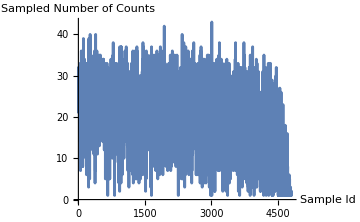
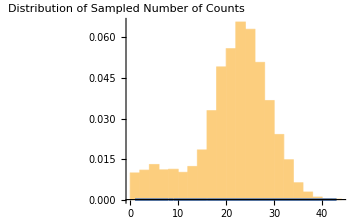
-Graphics-
-Graphics-
<|μ→20.7641,expected stddev→4.55677,n samples→4816,actual stddev→7.72634,total→100000,min→1,max→43|>

```mathematica
countsStats[sampledCubieCounts[0.001^(1/3),3,100000]]
```

In three dimensions, the number of deficient cubies is larger than “noticeable.”

#### SIX DIMENSIONS

<|Number of Cubies = →1000.|>

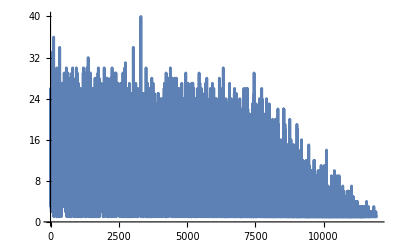
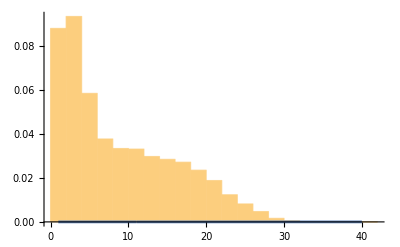
{-Graphics-,-Graphics-,<|μ→8.35282,√μ→2.89013,σ→7.07917,tot→100000,min→1,max→40|>}

```mathematica
countsStats[sampledCubieCounts[0.001^(1/6),6,100000]]
```

In six dimensions, the deficient cubies dominate the statistics.

#### TWENTY-SEVEN DIMENSIONS

<|Number of Cubies = →1000.|>

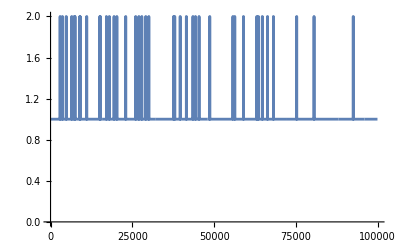
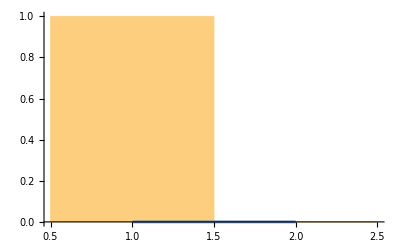
{-Graphics-,-Graphics-,<|μ→1.0004,√μ→1.0002,σ→0.0200001,tot→100000,min→1,max→2|>}

```mathematica
countsStats[sampledCubieCounts[0.001^(1/27),27,100000]]
```

In twenty-seven dimensions, virtually all the cubies are deficient.

There is no point in examining larger dimensions. To find cubies with non-zero populations (statistically), we must reduce the sizes of cubies, and thus increase their number and the computation time exponentially with dimension. It is not worth the computation time. We already have the shell method for verifying uniformity.

## STATISTICAL CONSTRUCTION

Alternatively to the geometrical constructions above, sample uniformly on the (d+2)-sphere (not in the (d+2)-ball), then delete any two coordinates of each point, deterministically or at random. We already know how to sample uniformly on the (d+2)-sphere: normalized multinormals. The following code illustrates generating uniforms in the 1-ball from uniforms on the 3-sphere by dropping two, randomly chosen coordinates:

```mathematica
ClearAll[sampleDBall2];
sampleDBall2[d_,n_,e_:2]:=
RandomSample[#,e]&/@(* random rejection *)
Normalize/@ (* uniform on the d-sphere *)
RandomVariate[
MultinormalDistribution[IdentityMatrix[d+e]],n];
```

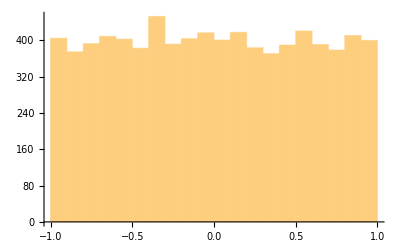

```mathematica
Histogram[Flatten[sampleDBall2[1,4000,2]]]
```

Why does this work? Why reject two coordinates at random, instead of one or three or seventeen?

First, realize that dropping one coordinate at random is the same as dropping the same coordinate from every point, at least for calculating the distribution of points, because all coordinates are sampled from the same distribution. Henceforth, we always drop the last two coordinates, z and y.

### THEOREM 1

The d-volume density of points is constant after projecting out z and y from a distribution constant per unit (d+2)-hyperspherical area.

### PROOF

We prove the theorem first for three dimensions, then argue by extension to dimensions greater than three.

Plan: produce a 2D distribution of points by dropping z. Next, drop the y coordinate by integrating it to produce a 1D density. Prove the resulting 1D density of points per unit of the x axis is independent of x.

As before, generate spherically uniform 3-vectors of unit length — on the 3-sphere — by sampling the 3-dimensional multinormal distribution, then normalizing the vectors:

```mathematica
show3D$[threeDPoints$=
Normalize/@
RandomVariate[
MultinormalDistribution[IdentityMatrix[3]],
40000]]
```

-Graphics3D-

Drop the z (last) coordinate of each point to produce a radially symmetric but non-uniform distribution in the 2-ball:

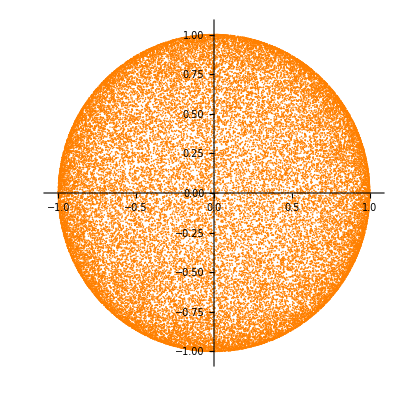

```mathematica
show2D$[(twoDPoints$=Drop[#,-1]&/@threeDPoints$)]
```

What is the 2D distribution at this step?

#### LEMMA 1

The 2D density of points is proportional to 1/√(1-r^2), where r<1 is the 2D distance from the origin. The density is unity near the origin and approaches infinity as r⟶1.

#### Proof of LEMMA 1:

Consider curved belts (or spherical segments) of equal z-height h on the surface of the unit 3-sphere surrounding the z axis. Each such belt has equal surface area 2π h by Archimedes' Hat-Box Theorem (also see Apostol, T., Mnatsakanian, M. (2004). A fresh look at the method of Archimedes. Am. Math. Monthly 111: 496–508. doi.org/10.2307/4145068, for much more.)

The following illustrates five belts in 3D:

```mathematica
Graphics3D[With[{dh=0.005,n=5,o={0,0,0}},
{Opacity[0.25],Sphere[],
Cone[{{0,0,#+dh},o},√(1-#^2)]&/@Range[0,1,1./n],
Cylinder[{o,{0,0,#+dh}},√(1-#^2)]&/@Range[0,1,1./n]}]]
```

-Graphics3D-

##### PROOF OF THE HAT-BOX THEOREM

The following shows a longitudinal cross-section of the 3-ball with belts of equal z-height.

A belt of z-height h corresponds to two elevation angles, θ_1<θ_2, such that sin θ_2-sin θ_1=h.

An element of area on the surface, in co-spherical coordinates, (θ (elevation),ϕ (azimuth)), via elevation (co-latitude) angles θ rather than the usual latitude angles, is cos θ dϕ dθ. The area of a belt is

```mathematica
∫_0^(2π) ∫_Subscript[θ, 1]^Subscript[θ, 2] Cos[θ]ⅆθⅆϕ
```

2 π (-Sin[θ_1]+Sin[θ_2])

which is 2πh.

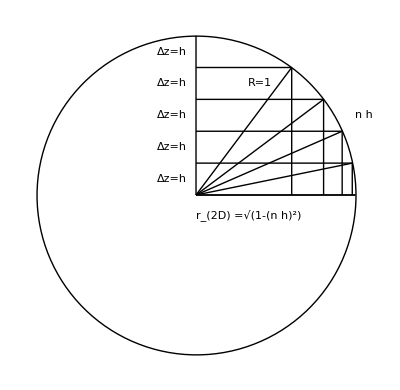

```mathematica
With[{o={0,0},N=5},
Graphics[{Circle[],
Text[Δz=h,{-0.15,#+0.5/N}]&/@Range[0,.99,1./N],
Text[n h,{1.05,0.5}],
Text[Subscript[r, 2D] =√(1-(n h)^2),{0.33,-.125}],
Text[R=1,{0.4,0.70}],
Line[{{0,#},{√(1-#^2),#}}&/@Range[0,.99,1./N]],
Line[{{√(1-#^2),0},{√(1-#^2),#}}&/@Range[0,.99,1./N]],
Line[{o,{√(1-#^2),#}}]&/@Range[0,1,1./N]}]]
```

QED Hat-Box Theorem ■

Back to lemma 1. The projected belts form annuli, or rings, in 2D. Consider the following projection of belts of z-height h=0.1 onto the 2D plane, along with the sample points, with their z coordinates dropped:

```mathematica
ClearAll[annuli];
annuli=Graphics@Circle[{0,0},√(1-#^2)]&/@Range[0,1,0.1];
Show[{show2D$[twoDPoints$]}~Join~annuli]
```

-Graphics-

The following illustrates a grouping function that isolates points in each annulus and shows a selection of one such group, the one whose maximum z-height is 0.8:

```mathematica
ClearAll[twoDPointsGroupedInAnnuli];
twoDPointsGroupedInAnnuli=GroupBy[twoDPoints$,Ceiling[√(1-Norm[#]^2),0.1]&];
Show[{show2D$[twoDPointsGroupedInAnnuli[0.8]]}~Join~annuli]
```

-Graphics-

The following illustrates that all annuli have, statistically, the same numbers of points.

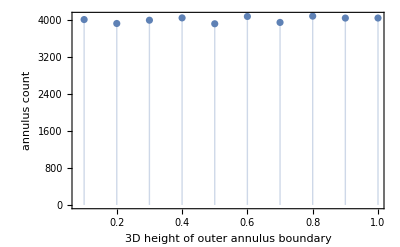

```mathematica
ListPlot[Length/@twoDPointsGroupedInAnnuli,
Filling->Axis,
PlotRange->{All,{0,All}},
Frame->True,
FrameLabel->{
{"annulus count",""},
{"3D height of outer annulus boundary","Annulus Count as a Function of Cell["z",ExpressionUUID->"7aba8c8e-68bd-48ae-be25-02e29bfdbf3b"]-height"}}]
```

The following illustrates the 2D widths and 2D areas of the annuli as a function of z-height:

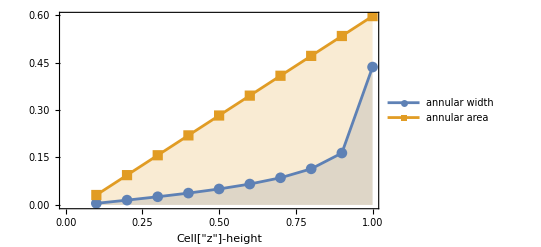

```mathematica
ListLinePlot[
With[{zs=Range[0,1,0.10]},
With[{rs=√(1-#^2)&/@zs},
{{Rest@zs,pairwise[#1-#2&,rs]}ᵀ,
{Rest@zs,pairwise[π(#1^2-#2^2)&,rs]}ᵀ}]],
Frame->True,PlotMarkers->Automatic,
FrameLabel->{{"",""},{"Cell["z",ExpressionUUID->"24788e15-f272-47aa-b6ab-08090297566e"]-height","Annular width and area versus Cell["z",ExpressionUUID->"e5418a73-8752-4334-9693-fb710b0b183d"]-height"}},
Filling->Axis,
PlotLegends->{"annular\nwidth","annular\narea"}]
```

Annular area is linear with z-height, and z-height varies as √(1-r^2). Point count per annular area is constant with z-height, so 2D point density against 2D r varies as 1/√(1-r^2).

QED Lemma 1 ■

Slice the circle vertically into bands of equal width Δx and y-height √(1-x^2):

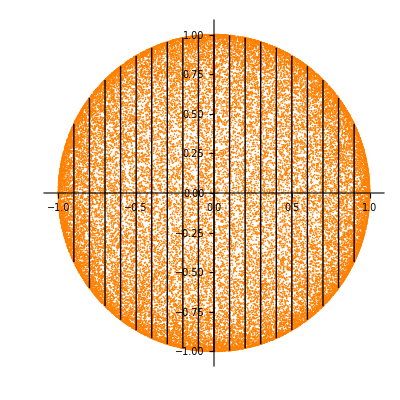

```mathematica
Show[{show2D$[twoDPoints$]}~Join~
(With[{y=√(1-#^2)},
Graphics@Line[{{#,-y},{#,y}}]]&/@Range[-1,1,0.1])]
```

Eliminate y by integrating the density over the each band:

```mathematica
∫_(-√(1-x^2))^(√(1-x^2)) 1/(√(1-y^2-x^2))ⅆy
```

ConditionalExpression[π, -1<Re[x]<1&&Im[x]==0]

independent of x.

There follow statistics for sampling 1,000,000 points according to this scheme of rejecting two coordinates for two dimensions and for 276 dimensions. As before, with a uniform distribution, we expect the standard deviations of counts to vary as the square root, 100, of the mean of the 10000 points in each annulus — the “eyeball” Chi-squared test for a uniform distribution.

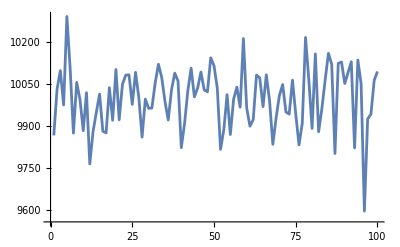
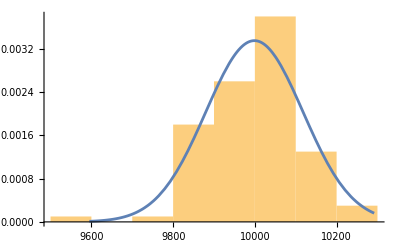
{-Graphics-,-Graphics-,<|μ→10000.,√μ→100.,σ→109.893,tot→1000000,min→9595,max→10292|>}

```mathematica
countsStats[sampledShellCounts2[0.01,2,1000000,sampleDBall2]]
```

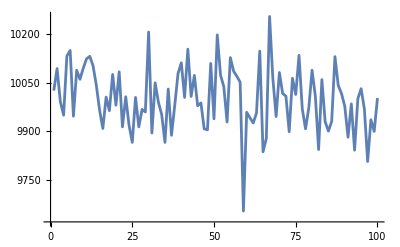
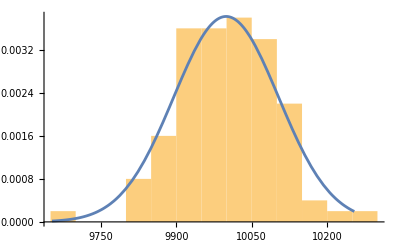
{-Graphics-,-Graphics-,<|μ→10000.,√μ→100.,σ→96.7453,tot→1000000,min→9653,max→10254|>}

```mathematica
countsStats[sampledShellCounts2[0.01,276,1000000]]
```

To extend the theorem to more dimensions, let x^2 stand for the Euclidean norm of all dimensions other than the last two. The integral still does not depend on x.

QED Theorem 1 ■